```mathematica
Norm[1+Exp[-0.5*I]]^2/2
```

1.87758

```mathematica
1+Cos[1]
```

1+Cos[1]

```mathematica
N[1+Cos[0.5]]
```

1.87758

```mathematica
data=Import["C:\\Users\\Nora\\Documents\\G1.5\\StrucFac\\plot.xlsx",{"Data",2}];
```

```mathematica
Dimensions[data]
```

{801,25}

## 2D square lattice

```mathematica
lattice2D = data[[All,1;;6]];
```

```mathematica
square100 = lattice2D[[All,{1,2}]];
```

```mathematica
square400 = lattice2D[[All,{1,3}]];
```

```mathematica
square625 = lattice2D[[All,{1,4}]];
```

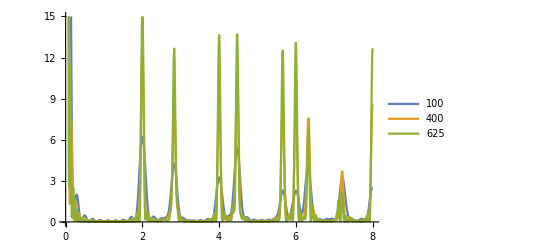

```mathematica
ListLinePlot[{square100,square400,square625},PlotRange->{0,15},PlotLegends->{"100","400","625"}]
```

```mathematica
sqcsv = Import["C:\\Users\\Nora\\Documents\\G1.5\\StrucFac\\squareLattice2D900.csv",{"Data"}]
```

{{0.,0.,900.},{0.,0.05,81.2238},{0.,0.1,40.8635},{0.,0.15,9.17486},{0.,0.2,1.76509×10^-30},{0.,0.25,3.41421},14630,{6.,5.8,6.54158×10^-26},{6.,5.85,9.17486},{6.,5.9,40.8635},{6.,5.95,81.2238},{6.,6.,900.}}
 |  |  |  |

```mathematica
ListPlot3D[sqcsv,PlotRange->{0,100}]
```

-Graphics3D-

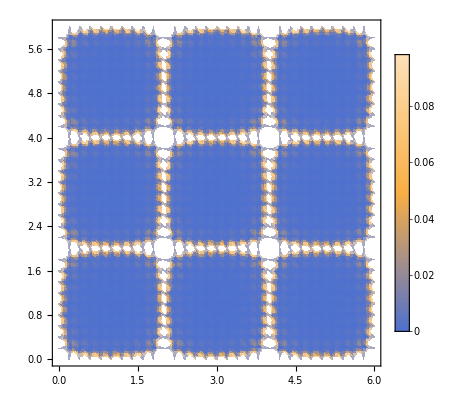

```mathematica
ListDensityPlot[sqcsv,PlotTheme->"Business"]
```

## 2D triangle lattice

```mathematica
triangle2D = data[[All,13;;21]];
```

```mathematica
triang100=triangle2D[[All,{1,2}]];
triang400 = triangle2D[[All,{1,3}]];
triang900 = triangle2D[[All,{1,4}]];
triang3600 = triangle2D[[All,{8,9}]];
```

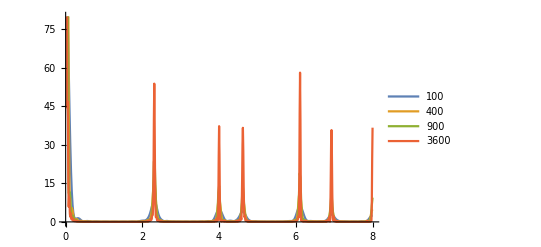

```mathematica
ListLinePlot[{triang100,triang400,triang900,triang3600},PlotRange->{0,80},PlotLegends->{"100","400","900","3600"}]
```

```mathematica
N[12/(Sqrt[3])]
```

6.9282

```mathematica
triangcsv = Import["C:\\Users\\Nora\\Documents\\G1.5\\StrucFac\\triangleLattice2D900.csv",{"Data"}]
```

{{0.,0.,900.},{0.,0.05,172.131},{0.,0.1,35.4309},{0.,0.15,0.630547},{0.,0.2,12.5743},{0.,0.25,4.42574},25910,{8.,7.8,0.846177},{8.,7.85,0.00709727},{8.,7.9,0.910988},{8.,7.95,0.592818},{8.,8.,0.0580487}}
 |  |  |  |

```mathematica
ListPlot3D[triangcsv,PlotRange->{0,100}]
```

-Graphics3D-

```mathematica
ListDensityPlot[triangcsv,Mesh->All,MeshFunctions->Automatic]
```

-Graphics-

## 2D ideal gas

```mathematica
ideal2D = data[[All,7;;11]];
```

```mathematica
ideal100 = ideal2D[[All,{1,2}]];
```

```mathematica
ideal225 = ideal2D[[All,{1,3}]];
```

```mathematica
ideal400 = ideal2D[[All,{1,4}]];
```

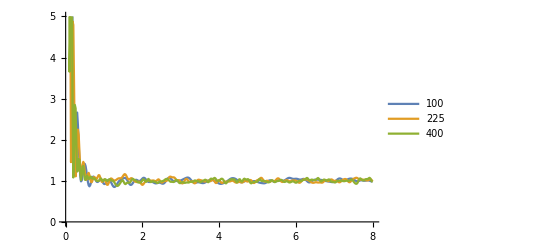

```mathematica
ListLinePlot[{ideal100,ideal225,ideal400},PlotRange->{0,5},PlotLegends->{"100","225","400"}]
```

## 1D lattice

```mathematica
data1D=Import["C:\\Users\\Nora\\Documents\\G1.5\\StrucFac\\plot.xlsx",{"Data",1}];
```

```mathematica
lat1D = data1D[[All,1;;5]];
```

```mathematica
lat1D5 = lat1D[[All,{1,2}]];
lat1D10 = lat1D[[All,{1,3}]];
```

```mathematica
lat1D20 = lat1D[[All,{1,4}]];
```

```mathematica
lat1D40 = lat1D[[All,{1,5}]];
```

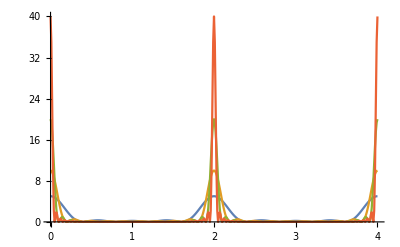

```mathematica
ListLinePlot[{lat1D5,lat1D10,lat1D20,lat1D40},PlotRange->{0,40}]
```

## 1D ideal gas

```mathematica
gas1D = data1D[[All,6;;10]];
```

```mathematica
gas1D5 = gas1D[[All,{1,2}]];
gas1D10 = gas1D[[All,{1,3}]];
```

```mathematica
gas1D40 = gas1D[[All,{1,4}]];
```

```mathematica
gas1D160 = gas1D[[All,{1,5}]];
```

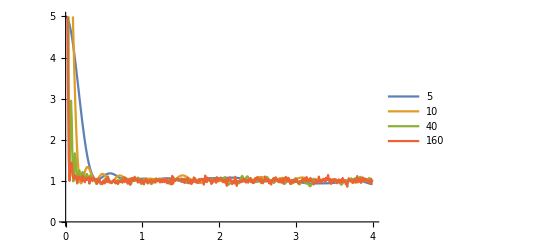

```mathematica
ListLinePlot[{gas1D5,gas1D10,gas1D40,gas1D160},PlotRange->{0,5},PlotLegends->{"5","10","40","160"}]
```